```mathematica
data=Import[ToFileName[NotebookDirectory[],"newdata.csv"],"CSV"];
rawdata[[1]]
```

{Number,Name,Country,Lat,Long,Height,Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

COLUMNS: “Number”,”Name”,”Country”,”Lat”,”Long”,”Height”,”Jan”,”Feb”,”Mar”,”Apr”,”May”,”Jun”,”Jul”,”Aug”,”Sep”,”Oct”,”Nov”,”Dec”}

```mathematica
temps = data[[All,7;;18]];
```

```mathematica
pc=PrincipalComponents[temps];
```

```mathematica
Variance[pc]
```

{1156.2,195.003,6.71966,2.50697,1.42176,0.47995,0.318722,0.199693,0.106251,0.0774372,0.0553304,0.0430945}

```mathematica
twopc=pc[[All,1;;2]];
```

```mathematica
pouplation = Map[CityData[ToLowerCase[#1],"Population"]&,data[[All,2;;3]]];
```

```mathematica
combined = Transpose[{data[[All,2]],twopc,pouplation}];
```

```mathematica
populationThr = 2000000;
```

```mathematica
combinedSmall = Select[combined,#[[3]]<populationThr  || !NumberQ[#[[3]]]&];
combinedLarge = Select[combined,#[[3]]>=populationThr &];
```

```mathematica
labeled=Map[Labeled[#[[2]],#[[1]]]&,combinedLarge];
```

```mathematica
tooltipped=Map[Tooltip[#[[2]],#[[1]]]&,combinedSmall];
```

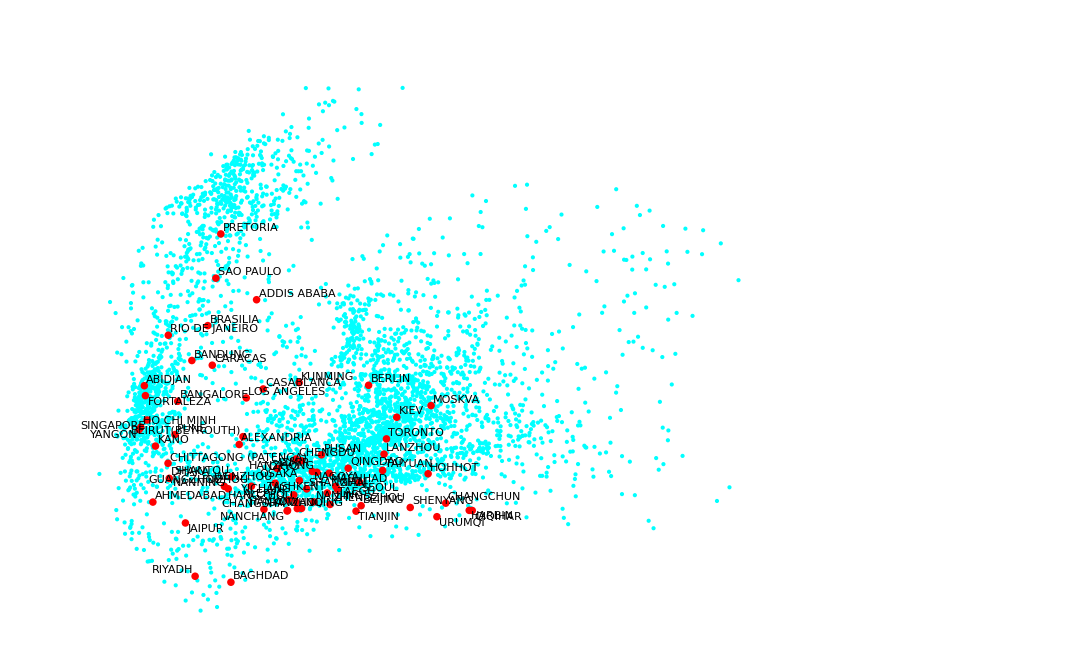

```mathematica
tplot=ListPlot[{tooltipped,labeled}, Axes->False,PlotStyle->{Cyan,Directive[Red,PointSize[0.005]]}]
```